Power Tower Truss

```mathematica
w1=7;w2=11;h1=7;h2=12;
```

```mathematica
θ1=ArcTan[h2/w1];θ2=ArcTan[h1/w2];θ3=ArcTan[h1/w1];
```

```mathematica
r1=0.7;r2=0.9;
```

```mathematica
truss=Graphics[{Thick,
(*DRAWING TRUSS*)
{EdgeForm@Thick,FaceForm@None,Polygon[{{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2},{w1,h1+h2},{-w1,h1+h2}}]},
{Line[{{#*w1,h1+h2},{0,2*h1+h2}}],Line[{{#*w1,h2},{0,h1+h2}}],Line[{{#*w1,0},{0,h2}}]}&/@{-1,1},
Line[{{#,h1+h2},{#,0}}]&/@{-w1,w1},
Line[{{-w1,h2},{w1,h2}}],

{GrayLevel@0.7,
Disk[{-w1,-0.75},0.75],Polygon[{{-w1-0.75,-0.75/2},{-w1+0.75,-0.75/2},{-w1+1,-2.5},{-w1-1,-2.5}}],
Disk[{w1,-r1},r1],Disk[{w1,-r1-r2},r2],Polygon[{{w1-r1,-0.65},{w1-0.875,-1.4},{w1+0.875,-1.4},{w1+r1,-0.65}}],
Black,
Line[{{-w1+#*0.75,-0.75},{-w1+#,-2.5}}]&/@{-1,1},Line[{{-w1-1,-2.5},{-w1+1,-2.5}}],Line[{#,√(0.75^2-(#+w1)^2)-0.75}&/@Range[-w1-0.75,-w1+0.75,0.1]],
Line[{#,√(r1^2-(#-w1)^2)-r1}&/@Range[w1-0.997*r1,w1+0.997*r1,0.001]],
Line[{#,-√(r2^2-(#-w1)^2)-r1-r2}&/@Range[w1-0.99*r2,w1+r2,0.01]],
Line[{{w1+#*r1,-0.65},{w1+#*0.875,-1.64}}]&/@{-1,1}}
},ImageSize->{600,400}];
```

```mathematica
labels=Graphics@{
Text[Framed[Style[Row@{" ",#1," "},16],RoundingRadius->15,FrameMargins->Tiny],#2,#3]&@@@{{"A",{-w1,0},{1.5,0}},{"B",{w1,0},{-1.75,0}},{"C",{w1,h2},{-1.5,0}},{"D",{w1,h1+h2},{-1.5,1}},{"E",{w1+w2,2*h1+h2},{-1,-1.2}},{"F",{0,2*h1+h2},{0,-1.2}},{"G",{-w1-w2,2*h1+h2},{1,-1.2}},{"H",{-w1,h1+h2},{1.5,1}},{" I ",{-w1,h2},{1.5,0}},{"J",{0,h1+h2},{0,-1.2}},{"K",{0,h2},{0,-1.2}}}};
```

```mathematica
Manipulate[
Module[{sol,RAx,RAy,RB,F1,F2,F3,F4,F5,F6,F7,F8,F9,F10,F11,F12,F13,F14,F15,F16,F17,F18,scale,colC,colT},
sol=Quiet@Chop@Solve[N@{
(*reactions*)rax+FEx==0,w2*ray+(2*h1+h2)*rax-(2*w1+w2)*rb+2*(w1+w2)*FEy==0,ray+rb-FG-FEy==0,
(*A*)f10*Cos[θ1]+RAx==0,f1+f10*Sin[θ1]+RAy==0,
(*B*)-f9*Cos[θ1]==0,f8+f9*Sin[θ1]+RB==0,
(*D*)-f15*Cos[θ3]-f16+f6*Cos[θ2]==0,-f7+f6*Sin[θ2]+f15*Sin[θ3]==0,
(*E*)-f6*Sin[θ2]-FEy==0,-f5-f6*Cos[θ2]+FEx==0,
(*F*)-f14*Sin[θ3]-f15*Sin[θ3]==0,-f4-f14*Cos[θ3]+f15*Cos[θ3]+f5==0,
(*G*)-FG-f3*Sin[θ2]==0,f3*Cos[θ2]+f4==0,
(*H*)-f3*Cos[θ2]+f13+f14*Cos[θ3]==0,f3*Sin[θ2]+f14*Sin[θ3]-f2==0,
(*I*)f11+f12*Cos[θ3]==0,
(*J*)-f12*Cos[θ3]-f13+f16+f17*Cos[θ3]==0,-f12*Sin[θ3]-f17*Sin[θ3]==0,
(*K*)-f10*Cos[θ1]-f11+f9*Cos[θ1]+f18==0
},{rax,ray,rb,f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13,f14,f15,f16,f17,f18}][[1]];

RAx=rax/.sol;RAy=ray/.sol;RB=rb/.sol;
F1=f1/.sol;F2=f2/.sol;F3=f3/.sol;F4=f4/.sol;F5=f5/.sol;F6=f6/.sol;F7=f7/.sol;F8=f8/.sol;F9=f9/.sol;
F10=f10/.sol;F11=f11/.sol;F12=f12/.sol;F13=f13/.sol;F14=f14/.sol;F15=f15/.sol;F16=f16/.sol;
F17=f17/.sol;F18=f18/.sol;

scale[F_]:=3+10*Rescale[Abs@F,{0,25.7}];
colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

Show[truss,If[label,labels,{}],PlotRange->{{-22,29},{-15,32.5}},Epilog->{
Flatten@{Thickness@0.007,Which[#1<0,{colC,Arrowheads@{-0.045,0.045}},#1>0,{colT,Arrowheads@{{0.045,0.315},{-0.045,0.675}}},#1==0,Black],If[#1==0,Line,Arrow]@#2}&@@@{
{F1,{{-w1,0},{-w1,h2}}},{F2,{{-w1,h2},{-w1,h1+h2}}},{F3,{{-w1,h1+h2},{-w1-w2,2*h1+h2}}},{F4,{{-w1-w2,2*h1+h2},{0,2*h1+h2}}},{F5,{{0,2*h1+h2},{w1+w2,2*h1+h2}}},{F6,{{w1,h1+h2},{w1+w2,2*h1+h2}}},{F7,{{w1,h2},{w1,h1+h2}}},{F8,{{w1,0},{w1,h2}}},{F9,{{w1,0},{0,h2}}},{F10,{{-w1,0},{0,h2}}},{F11,{{-w1,h2},{0,h2}}},{F12,{{-w1,h2},{0,h1+h2}}},{F13,{{-w1,h1+h2},{0,h1+h2}}},{F14,{{-w1,h1+h2},{0,2*h1+h2}}},{F15,{{w1,h1+h2},{0,2*h1+h2}}},{F16,{{0,h1+h2},{w1,h1+h2}}},{F17,{{w1,h2},{0,h1+h2}}},{F18,{{w1,h2},{0,h2}}}},

Text[Rotate[Style[If[#1==0,0,NumberForm[Abs@#1,{5,1}]],17,Which[#1<0,colC,#1>0,colT,#1==0,Black],Background->White],#4],#3]&@@@{{F1,"1,AI",{-w1,h2/2},π/2},{F2,"6,HI",{-w1,h2+h1/2},π/2},{F3,"3,GH",{-w1-w2/2,1.5*h1+h2},-θ2},{F4,"3,FG",{-(w1+w2)/2,2*h1+h2},0},{F5,"4,EF",{(w1+w2)/2,2*h1+h2},0},{F6,"4,DE",{w1+0.5*w2,1.5*h1+h2},θ2},{F7,"7,CD",{w1,0.5*h1+h2},π/2},{F8,"2,BC",{w1,0.5h2},π/2},{F9,"2,BK",{0.5*w1,h2/2},-θ1},{F10,"1,AK",{-0.5*w1,0.5*w2},θ1},{F11,"9,IK",{-0.5*w1,h2},0},{F12,"9,IJ",{-0.5*w1,0.5*h1+h2},θ3},{F13,"6,HJ",{-0.5*w1,h1+h2},0},{F14,"5,FH",{-0.5*w1,1.5*h1+h2},θ3},{F15,"5,DF",{0.5*w1,1.5*h1+h2},-θ3},{F16,"7,DJ",{0.5*w1,h1+h2},0},{F17,"8,CJ",{0.5*w1,0.5*h1+h2},-θ3},{F18,"8,CK",{0.5*w1,h2},0}},

{Blue,Thickness@0.01,Arrowheads@0.05,
Arrow[{{-(w1+w2),2*h1+h2},{-(w1+w2),2*h1+h2-scale[FG]}}],
Arrow[{{w1+w2,2*h1+h2},{w1+w2,2*h1+h2-scale[FEy]}}],
If[FEx≠0,Arrow[{{w1+w2,2*h1+h2},{w1+w2+scale[FEx],2*h1+h2}}]],
Arrow[If[RAy<0,Reverse,N]@{{-w1,-0.75-scale[RAy]},{-w1,-0.75}}],If[FEx≠0,Arrow[{{-w1+scale[RAx],-0.1*h1},{-w1,-0.1*h1}}]],
Arrow[{{w1,-0.75-scale[RB]},{w1,-0.1*h1}}],
Text[Style[If[label,Subscript[Style["F",Italic],"G"],Row@{NumberForm[Abs@FG,{5,1}]," kN"}],18],{-w1-w2,2*h1+h2-scale[FG]},{0,1.5}],
Text[Style[If[label,Subscript[Style["F",Italic],Row@{"E,",Style[#2,Italic]}],Row@{NumberForm[Abs@#1,{5,1}]," kN"}],18],#3,#4]&@@@{
{FEy,"y",{w1+w2,2*h1+h2-scale[FEy]},{0,1.5}},If[FEx≠0,{FEx,"x",{w1+w2+scale[FEx],2*h1+h2},{-1.2,0}}]},
Text[Style[If[label,Subscript[Style["R",Italic],Row@{"A,",Style[#2,Italic]}],Row@{NumberForm[Abs@#1,{5,1}]," kN"}],18],#3,#4]&@@@{
If[RAx≠0,{RAx,"x",{-w1+scale[RAx],-0.75},{-1.2,0}}],{RAy,"y",{-w1,-0.75-scale[RAy]},{0,1.5}}(*,{RB,{w1,-0.75-scale[RB]},{0,1.5}}*)},
Text[Style[If[label,Subscript[Style["R",Italic],"B"],Row@{NumberForm[Abs@RB,{5,1}]," kN"}],18],{w1,-0.75-scale[RB]},{0,1.5}]},

{PointSize@0.02,Point@#,White,PointSize@0.012,Point@#}&/@{{-w1,-0.75},{-w1,h2},{-w1,h1+h2},{-w1-w2,2*h1+h2},{w1,-0.75},{w1,h2},{w1,h1+h2},{w1+w2,2*h1+h2},{0,h2},{0,h1+h2},{0,2*h1+h2}},

Text[Style[Row@{"all ",Style["compression",colC]," and ",Style["tension",colT]," forces are in kN"},17,GrayLevel@0.4],{0,31.5}]
}]
],
Grid[{
{"forces at joint E (kN)",
Control[{{FEx,1.8,Row@{"horizontal ",Subscript[Style["F",Italic],Row@{"E,",Style["x",Italic]}]}},0,4,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{FEy,8,Row@{"vertical ",Subscript[Style["F",Italic],Row@{"E,",Style["y",Italic]}]}},4,10,0.1,Appearance->"Labeled",ImageSize->Small}]},
{Control[{{FG,5,"force at joint G (kN)"},4,10,0.1,Appearance->"Labeled"}],SpanFromLeft,
Control[{{label,False,"show joint labels"},{True,False}}]}
},Alignment->Left],
SaveDefinitions->True]
```

The method of joints is used to solve for the member forces and reaction forces on a power tower truss. Use sliders to set the point load forces at joints G and E, and check "show joint labels" to see the labeled joints. This truss rests on one pinned support (A, left) and one roller support (B, right). The pinned support resists both vertical and horizontal forces, whereas the roller only resists vertical forces. Member forces are shown in kN. Arrows that point outward (green) represent the member response to compression forces, and arrows that point inward (red) represent the member response to tension forces. Compression acts to shorten the member and tension acts to lengthen the member. Zero members are shown as black lines. Zero members are members that are neither in tension nor in compression, so the force is 0 kN. The purpose of zero members is to provide stability and extra support to the structure in case another member fails.

The reaction forces are calculated first by summing the x-forces, then calculating moments about joint G, and the doing a force balance in the y-direction.

∑F_x=0=R_(A,x)+F_(E,x),

∑M_G=0=w_2 R_(A,y)+(2 h_1+h_2) R_(A,x)-(2 w_1+w_2) R_B+2 (w_1+w_2) F_(E,y),

∑F_y=0=R_(A,y)+R_B-F_G-F_(E,y),

where R_(A,x) and R_(A,y) are the reaction forces in the x and y directions at joint A, R_B is the reaction force at joint B, F_(E,x) and F_(E,y) are the point load forces in the x and y directions at joint E, F_G is the point load force at joint G, w_1 and w_2 are the shorter and longer widths, and h_1 and h_2 are the shorter and longer heights. The first, second, and fourth terms in the moment balance (w_2 R_(A,y), (2 h_1+h_2) R_(A,x), and 2 (w_1+w_2) F_(E,y)) are positive because they cause a clockwise rotation, and the third term (-(2 w_1+w_2) R_B) is negative because it causes a counterclockwise rotation.

The method of joints is used to calculate the member forces using the order of the calculations below. Force balances are done assuming we can determine which forces are under tension and which forces are under compression prior to solving the truss. At joint A there is an upward force of R_(A,y) so we know that F_1 must be a compression force in order for the truss to remain stationary. Also, there is a force of R_(A,x) in the negative x direction so F_10 must be a tension force. A labeled truss is shown in Figure 1 below.

Joint G:
θ_2=tan^-1(h_1/w_2),
∑F_y=0=-F_G+F_3 sin θ_2,
∑F_x=0=-F_3 cos θ_2+F_4.

Joint E:

∑F_y=0=F_6 sin θ_2-F_(E,y),

∑F_x=0=-F_5+F_6 cos θ_2+F_(E,x).

Joint F:

θ_3=tan^-1(h_1/w_1),

∑F_y=0=-F_14 sin θ_3+F_15 sin θ_3,

∑F_x=0=-F_4+F_5-F_14 cos θ_3-F_15 cos θ_3.

Joint H:

∑F_x=0=F_3 cos θ_2-F_13+F_14 cos θ_3,

∑F_y=0=-F_3 sin θ_2+F_14 sin θ_3.

Joint D:

∑F_x=0=-F_6 cos θ_2+F_15 cos θ_3+F_16,

∑F_y=0=-F_6 sin θ_2+F_7-F_15 sin θ_3.

Joint J:

∑F_x=0=-F_12 cos θ_3+F_13-F_16-F_17 cos θ_3,

∑F_y=0=-F_12 sin θ_3+F_17 sin θ_3.

Joint A:

θ_1=tan^-1(h_2/w_1),

∑F_x=0=F_10 cos θ_1+R_(A,x),

∑F_y=0=-F_1+F_10 sin θ_1+R_(A,y).

Joint B:

∑F_x=0=F_9 cos θ_1 → F_9=0 kN,

∑F_y=0=-F_8+F_9 sin θ_1+R_B.

Joint I:

∑F_x=0=-F_11+F_12 cos θ_3.

Joint C:

∑F_x=0=F_17 cos θ_3-F_18.

Figure 1

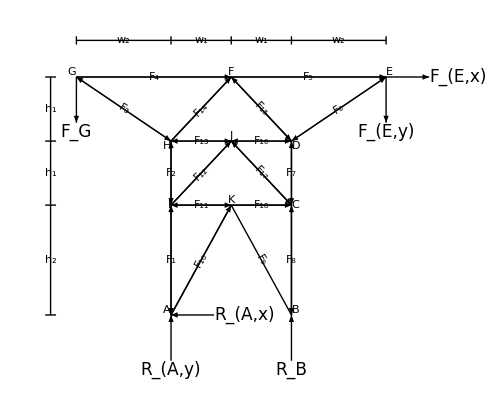

Reference

[1] Engineering Mechanics Statics 12th ed., New Jersey: Pearson Education Inc., 2010.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

mechanical engineering

civil engineering

statics

mechanics

method of joints

truss

member forces

compression force

tension force

zero member

Contributed by: Rachael L. Baumann

Additional contributions by: John L. Falconer

(University of Colorado Boulder, Department of Chemical and Biological Engineering)